```mathematica
X[v_,t_,θ_]:=v t Cos[θ]
```

```mathematica
Y[v_,t_,θ_]:=v t Sin[θ]-(1/2)(9.81) t^2+100
```

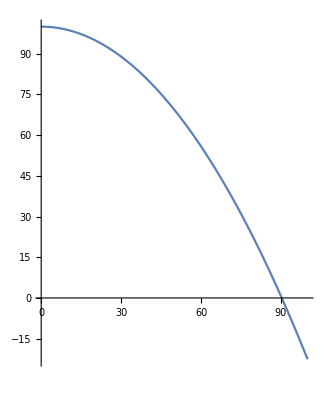

```mathematica
ParametricPlot[{X[20,t,0],Y[20,t,0]},{t,0,5}]
```

```mathematica
F[g_,h0_,v_,x_,θ_]:=v(x/(v Cos[θ]))(Sin[θ])-(g/2)(x/(v Cos[θ]))^2+h0
```

```mathematica
F[9.81,100,20,90,0]
```

0.67375

```mathematica
Solve[F[9.81,100,20,x,0]==0,x]
```

{{x→-90.3047},{x→90.3047}}

```mathematica
NumberForm[π NIntegrate[F[9.81,100,20,x,0],{x,0,90.3047},AccuracyGoal->5]^2,16]
```

1.138644975816562×10^8

```mathematica
113864497.5817
```

1.13864×10^8

```mathematica
IntegerPart[1.1386449758165613*^8]
```

113864497

```mathematica
113864497.5816562
```

1.13864×10^8